```mathematica
ListDevices[jfile_List]:=Module[{log},
log="log"/.jfile;
Select[DeleteDuplicates[("device"/.#)&/@log],#≠"device"&]
];
GetDeviceLog[deviceName_String,jfile_List]:=Module[{log},
log="log"/.jfile;
Select[log,("device"/.#)==deviceName&]
];
getVar[s_String,deviceLog_List,timeFit_FittedModel]:=
Module[{dList,vList},
dList=("data"/.#)& /@ deviceLog;
vList = Select[(s/.#)& /@ dList,Head[#]==List&];
{timeFit @("vartime"/.#), ("value"/.#)}& /@ vList
];
getAllVars[deviceLog_List,timeFit_FittedModel]:=
Module[{varList,dlist},
dlist=("data"/.#)& /@ deviceLog;
varList=Union[Table[i[[1]],{i,Select[Flatten[dlist],Head[#[[2]]]==List&]}]];
{varList,Table[DeleteDuplicates[getVar[v,deviceLog,timeFit]],{v,varList}]}
];
GetDeviceData[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13];
getAllVars[dev,timeFit]
];
GetTimeFit[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{deviceTimes,devServerTimes}],x,x,WorkingPrecision->13]
];
```

```mathematica
GetDevLines[deviceName_String,jfile_List]:=Module[{log,baseServerTime},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
Select[log,("device"/.#)==deviceName&]
]
```

```mathematica
ShowCommands[jf_List]:=Module[{cmd},
cmd=GetDeviceData["Command",jf];
TableForm[cmd[[2,3]]]
]
```

```mathematica
PlotTimes[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
ListPlot[Transpose[{devServerTimes,deviceTimes}]]
];
```

```mathematica
GetDevTimes[deviceName_String,jfile_List]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
"devicetime"/.("data"/.#)&/@dev
];
```

```mathematica
hvTimes=GetDevTimes["HV-LOWSIDE",jfile1];
```

```mathematica
FindBreaks[x_]:=Module[{b,n,i},
b={};
n=Length[x];
For[i=1, i<n,i++,
If[x[[i]]>x[[i+1]],AppendTo[b,i]]
];
b
]
```

```mathematica
GetDeviceDataRange[deviceName_String,jfile_List,toTake_]:=Module[{log,dev,baseServerTime,timeFit,devServerTimes,deviceTimes},
{log,baseServerTime}={"log","base-timestamp"}/.jfile;
dev=Select[log,("device"/.#)==deviceName&];
devServerTimes=("servertime"/.#&/@dev)-baseServerTime;
deviceTimes="devicetime"/.("data"/.#)&/@dev;
timeFit = LinearModelFit[Transpose[{Take[deviceTimes,toTake],Take[devServerTimes,toTake]}],x,x,WorkingPrecision->13];
getAllVars[Take[dev,toTake],timeFit]
];
```

```mathematica
name
```

c:\git\FusorExperiments\logs\keep\fusor-2022-07-24T14-55-33_low voltage at 10 microns.json

```mathematica
jfile4=Import[name]
```

{base-timestamp→1658533369845,instant→2022-07-22T16:42:49,log→{{device→<reset>,data→{},servertime→1658533369845},{device→TMP,data→{error→{value→0,vartime→281129},pump_curr_amps→{value→0.,vartime→281129},pump_freq→{value→0.,vartime→281129},devicetime→281137},servertime→1658533369866},12373,{device→SENSORARRAY,data→{hfm→{value→0.,vartime→657441},devicetime→657459},servertime→1658533747627},{}}}
 |  |  |  |

```mathematica
jfile5=Import[name]
```

{base-timestamp→1658700977254,instant→2022-07-24T15:16:17,log→{{device→<reset>,data→{},servertime→1658700977254},{device→PIRANI,data→{p3→{value→0.00964,vartime→1332554},p4→{value→0.00964,vartime→1332619},devicetime→1332719},servertime→1658700977286},9288,{device→SENSORARRAY,data→{hfm→{value→0.,vartime→1588199},devicetime→1588275},servertime→1658701231153},{}}}
 |  |  |  |

```mathematica
jfile6=Import[name]
```

{base-timestamp→1658701461153,instant→2022-07-24T15:24:21,log→{{device→<reset>,data→{},servertime→1658701461153},{device→SENSORARRAY,data→{hfm→{value→0.,vartime→1818051},devicetime→1818128},servertime→1658701461188},{device→PIRANI,data→{p2→{value→-763.,vartime→1816095},devicetime→1816121},servertime→1658701461189},7092,{device→SENSORARRAY,data→{hfm→{value→0.,vartime→2025072},devicetime→2025160},servertime→1658701668385},{}}}
 |  |  |  |

```mathematica
tmpLines6=GetDevLines["TMP",jfile6];
```

```mathematica
Take[tmpLines6,{1270,1280}]
```

{{device→TMP,data→{error→{value→0,vartime→1969769},pump_curr_amps→{value→0.00976563,vartime→1969769},pump_freq→{value→0.,vartime→1969769},devicetime→1969776},servertime→1658701611236},{device→TMP,data→{error→{value→0,vartime→1969995},pump_curr_amps→{value→0.00732422,vartime→1969995},pump_freq→{value→0.,vartime→1969995},devicetime→1970002},servertime→1658701611458},{device→TMP,data→{error→{value→0,vartime→1970112},pump_curr_amps→{value→0.00976563,vartime→1970112},pump_freq→{value→0.,vartime→1970112},devicetime→1970119},servertime→1658701611580},{device→TMP,data→{error→{value→0,vartime→1970227},pump_curr_amps→{value→0.00732422,vartime→1970227},pump_freq→{value→0.,vartime→1970227},devicetime→1970234},servertime→1658701611690},{device→TMP,data→{tmp→{value→True,vartime→1719280},lowspeed→{value→False,vartime→0},error→{value→0,vartime→1970341},reset→{value→False,vartime→1711293},pump_curr_amps→{value→0.00732422,vartime→1970341},pump_freq→{value→0.,vartime→1970341},devicetime→1970353},servertime→1658701611823},{device→TMP,data→{tmp→{value→False,vartime→1},lowspeed→{value→False,vartime→1},error→{value→0,vartime→1379},reset→{value→False,vartime→1},pump_curr_amps→{value→0.00244141,vartime→1379},pump_freq→{value→0.,vartime→1379},devicetime→1390},servertime→1658701615409},{device→TMP,data→{error→{value→0,vartime→1506},pump_curr_amps→{value→0.00244141,vartime→1506},pump_freq→{value→0.,vartime→1506},devicetime→1513},servertime→1658701615522},{device→TMP,data→{error→{value→0,vartime→1618},pump_curr_amps→{value→0.00244141,vartime→1618},pump_freq→{value→0.,vartime→1618},devicetime→1626},servertime→1658701615635},{device→TMP,data→{error→{value→0,vartime→1734},pump_curr_amps→{value→0.00244141,vartime→1734},pump_freq→{value→0.,vartime→1734},devicetime→1741},servertime→1658701615749},{device→TMP,data→{tmp→{value→False,vartime→1},lowspeed→{value→False,vartime→1},error→{value→0,vartime→1301},reset→{value→False,vartime→1},pump_curr_amps→{value→0.,vartime→1300},pump_freq→{value→0.,vartime→1301},devicetime→1311},servertime→1658701631759},{device→TMP,data→{error→{value→0,vartime→1432},pump_curr_amps→{value→0.,vartime→1431},pump_freq→{value→0.,vartime→1432},devicetime→1438},servertime→1658701631874}}

```mathematica
GetDeviceData["TMP",jfile6]
```

{{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp},{{{80696.1962744,0},{80688.6748055,0},{80681.8997419,0},{80675.2395099,0},1580,{183018.144424,0},{183011.65644,0},{183005.168455,0},{182998.450807,0}},4,{{44,True},{45,5}}}}
 |  |  |  |

```mathematica
FindBreaks[GetDevTimes["TMP",jfile6]]
```

{1274,1278}

```mathematica
tmp6a=GetDeviceDataRange["TMP",jfile6,1274]
```

{{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp},{{{36.14529,0},{167.08798,0},{285.03637,0},{400.985622,0},{517.934442,0},1264,{150300.38537,0},{150417.33419,0},{150532.28389,0},{150646.23402,0}},4,{{1}}}}
 |  |  |  |

```mathematica
Take[tmp6a[[2,6]],-50]
```

Take::take: Cannot take positions -50 through -1 in {{-100304.94259,True}}.

Take[{{-100304.94259,True}},-50]

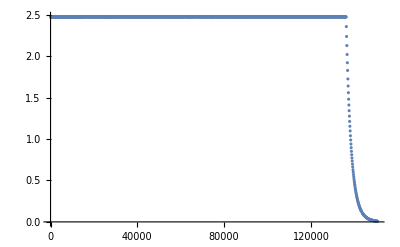

```mathematica
ListPlot[tmp6a[[2,3]],PlotRange->All]
```

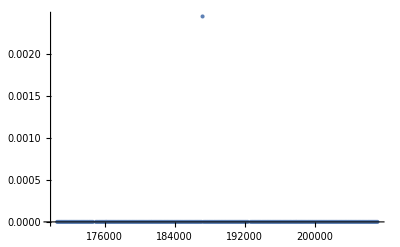

```mathematica
ListPlot[tmp6c[[2,3]],PlotRange->All]
```

```mathematica
tmp6c=GetDeviceDataRange["TMP",jfile6,1278-1589]
```

```mathematica
Dimensions[GetDevTimes["TMP",jfile6]]
```

{1589}

```mathematica
ShowCommands[jfile4]
```

11550. | TMP low
54044. | Solenoid open
58060. | Set needle valve:10.0
58166. | Set needle valve:10.0
81916. | Set needle valve:20.0
81999. | Set needle valve:20.0
92369. | Set needle valve:10.0
92636. | Set needle valve:10.0
106250. | variac:set:40
106390. | variac:set:40
168790. | TMP on
206360. | TMP off
215530. | TMP on
246360. | TMP off
254360. | TMP on
267010. | variac:set:0
320230. | Solenoid closed

```mathematica
ShowCommands[jfile5]
```

21350. | Solenoid open
24410. | Set needle valve:40.0
24530. | Set needle valve:40.0
57119. | Set needle valve:60.0
57237. | Set needle valve:60.0
84569. | variac:set:40
84620. | HV on
86823. | variac:set:40
128740. | Set needle valve:50.0
128850. | Set needle valve:50.0
150350. | Set needle valve:45.0
150470. | Set needle valve:45.0
175540. | Set needle valve:40.0
175620. | Set needle valve:40.0
187500. | Set needle valve:38.0
187600. | Set needle valve:38.0
210190. | Set needle valve:0.0
210250. | Set needle valve:0.0
221570. | TMP on
237040. | variac:set:0

```mathematica
ShowCommands[jfile6]
```

19590. | Set needle valve:35.0
19680. | Set needle valve:35.0
20590. | Solenoid open
29860. | Set needle valve:50.0
29940. | Set needle valve:50.0
37724. | Set needle valve:60.0
37807. | Set needle valve:60.0
48173. | variac:set:40
71523. | Set needle valve:50.0
71640. | Set needle valve:50.0
83946. | Set needle valve:45.0
84051. | Set needle valve:45.0
114590. | Set needle valve:40.0
114770. | Set needle valve:40.0
132670. | Set needle valve:37.0
132790. | Set needle valve:37.0
146850. | Set needle valve:20.0
146880. | Set needle valve:20.0
180180. | variac:set:0
194060. | Solenoid closed
198190. | Set needle valve:0.0

```mathematica
ListDevices[jfile6]
```

{<reset>,SENSORARRAY,PIRANI,TMP,GAS,HV-LOWSIDE,VARIAC,Heartbeat,Command}

```mathematica
FindBreaks[GetDevTimes["HV-LOWSIDE",jfile6]]
```

{1254}

```mathematica
FindBreaks[GetDevTimes["Commands",jfile6]]
```

{}

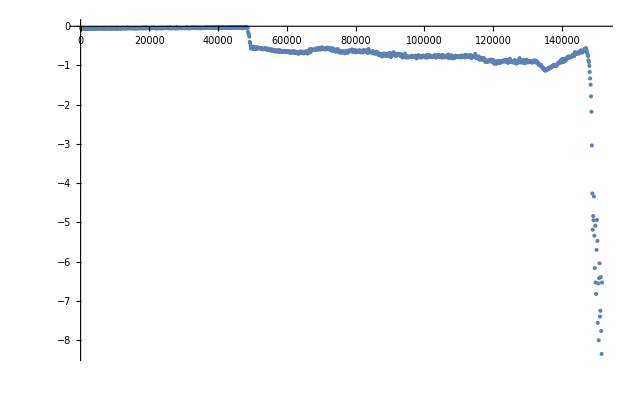

```mathematica
ShowHvRange[jfile6,1254]
```

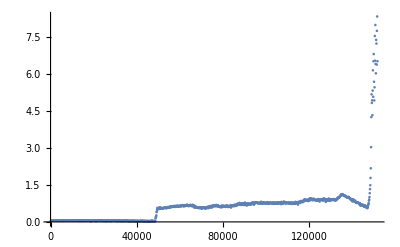

```mathematica
ShowHvRangeInv[jfile6,1254]
```

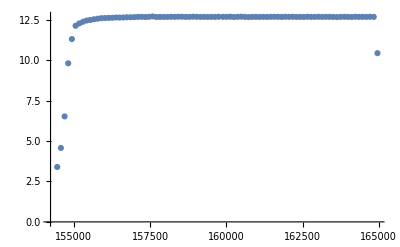

```mathematica
ShowHvRangeInv[jfile6,-89]
```

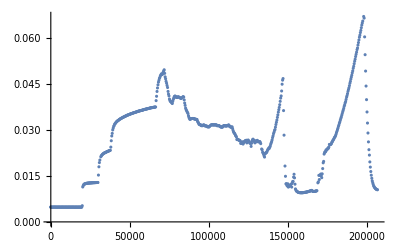

```mathematica
ShowPressure[jfile6]
```

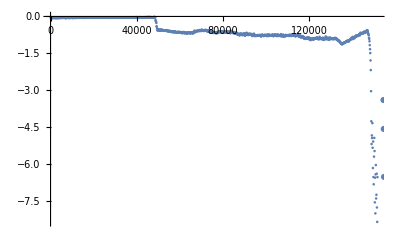

```mathematica
Show[Out[221],Out[223]]
```

```mathematica
Dimensions[GetDevTimes["HV-LOWSIDE",jfile6]]
```

{1343}

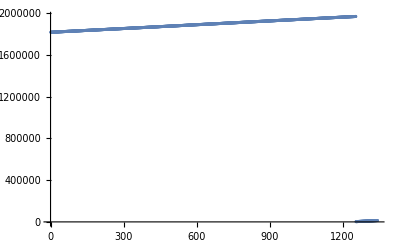

```mathematica
ListPlot[GetDevTimes["HV-LOWSIDE",jfile6],PlotRange->All]
```

```mathematica
hvTimes=GetDevTimes["HV-LOWSIDE",jfile6];
```

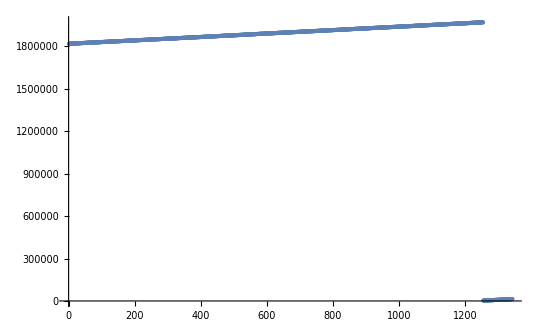

```mathematica
ListPlot[hvTimes,PlotRange->All]
```

```mathematica
Take[hvTimes,-200]
```

{1956850,1956972,1957094,1957217,1957339,1957462,1957583,1957708,1957830,1957953,1958075,1958198,1958320,1958443,1958564,1958687,1958809,1958831,1958953,1959075,1959198,1959320,1959443,1959565,1959688,1959810,1959932,1960054,1960177,1960299,1960422,1960544,1960667,1960788,1960911,1961033,1961156,1961278,1961401,1961524,1961646,1961768,1961890,1962013,1962135,1962260,1962383,1962505,1962628,1962750,1962872,1962995,1963117,1963240,1963362,1963485,1963607,1963628,1963751,1963874,1963997,1964119,1964241,1964363,1964486,1964608,1964731,1964853,1964976,1965097,1965220,1965342,1965465,1965587,1965710,1965832,1965955,1966076,1966199,1966321,1966443,1966566,1966688,1966811,1966935,1967057,1967179,1967301,1967424,1967546,1967668,1967791,1967912,1968035,1968157,1968279,1968301,1968423,1968546,1968678,1968801,1968923,1969046,1969168,1969290,1969413,1969534,1969656,1969779,1969901,1970023,2667,2787,2908,3028,3148,3269,3390,3511,3632,3752,3872,3992,4113,4233,4354,4473,4594,4714,4834,4955,5074,5195,5315,5436,5556,5676,5796,5919,6039,6159,6280,6400,6520,6640,6760,6881,7001,7121,7241,7361,7482,7602,7723,7842,7963,7983,8103,8224,8344,8465,8585,8705,8825,8945,9066,9186,9306,9426,9546,9667,9787,9908,10028,10148,10269,10390,10511,10632,10753,10873,10994,11115,11238,11359,11480,11600,11721,11842,11963,12084,12205,12325,12446,12567,12689,12809,12930,13050,13172}

```mathematica
hv6a=GetDeviceDataRange["HV-LOWSIDE",jfile6,1254]
```

{{cw_avg,cwc_avg,nst_rms,variac_rms},{{{119.42333,-0.0558405},{240.39775,-0.0570113},{384.367317,-0.0587673},{507.341319,-0.066377},1212,{151407.44036,-7.7665},{151529.41457,-8.35224},{151652.38858,-6.53225}},2,{{40,0.274107},1217,{1}}}}
 |  |  |  |

```mathematica
hv6b=GetDeviceDataRange["HV-LOWSIDE",jfile6,-89]
```

{{cw_avg,cwc_avg,nst_rms,variac_rms},{{{154451.4106801,-3.39723},{154572.3970777,-4.57324},{154693.3834754,-6.52262},{154812.3700979,-9.8051},{154933.3564956,-11.3037},{155054.3428933,-12.1258},{155175.3292909,-12.271},{155296.3156886,-12.373},{155417.3020863,-12.4514},{155536.2887088,-12.4853},{155657.2751064,-12.5287},{155777.2616165,-12.5603},{155898.2480142,-12.5983},{156018.2345243,-12.6042},{156138.2210344,-12.6141},{156258.2075444,-12.6194},{156379.1939421,-12.6375},{156499.1804522,-12.6329},{156619.1669623,-12.6399},{156740.1533599,-12.6533},{156859.1399824,-12.6539},{156980.1263801,-12.6604},{157100.1128902,-12.675},{157221.0992879,-12.6779},{157341.085798,-12.6662},{157460.0724205,-12.6779},{157581.0588181,-12.7019},{157704.044991,-12.6691},{157824.031501,-12.6732},{157944.0180111,-12.6721},{158065.0044088,-12.6721},{158183.9910313,-12.6826},{158303.9775414,-12.6773},{158424.9639391,-12.6838},{158544.9504491,-12.685},{158665.9368468,-12.6744},{158785.9233569,-12.6773},{158904.9099794,-12.6891},{159025.8963771,-12.6809},{159145.8828871,-12.6744},{159266.8692848,-12.675},{159386.8557949,-12.6715},{159505.8424174,-12.6768},{159626.8288151,-12.6738},{159746.8153252,-12.6832},{159887.7994745,-12.6785},{160008.7858722,-12.6779},{160128.7723823,-12.6861},{160248.7588923,-12.6674},{160369.74529,-12.6791},{160488.7319125,-12.689},{160609.7183102,-12.6756},{160729.7048203,-12.6633},{160849.6913303,-12.675},{160970.677728,-12.6762},{161090.6642381,-12.6727},{161210.6507482,-12.6773},{161330.6372583,-12.6715},{161451.6236559,-12.6791},{161571.610166,-12.6814},{161691.5966761,-12.6791},{161811.5831862,-12.6721},{161932.5695839,-12.6826},{162053.5559815,-12.6768},{162174.5423792,-12.6832},{162295.5287769,-12.6732},{162416.5151745,-12.6738},{162536.5016846,-12.6715},{162657.4880823,-12.6826},{162778.47448,-12.6744},{162899.4608776,-12.6738},{163022.4470505,-12.6814},{163143.4334481,-12.6727},{163263.4199582,-12.6785},{163384.4063559,-12.6779},{163505.3927536,-12.6738},{163626.3791512,-12.6651},{163747.3655489,-12.675},{163868.3519466,-12.6797},{163988.3384566,-12.6744},{164109.3248543,-12.6703},{164230.311252,-12.6838},{164351.2976497,-12.6744},{164472.2840473,-12.6773},{164593.270445,-12.6744},{164713.2569551,-12.6832},{164834.2433527,-12.6738},{164956.229638,-10.4319}},{{154451.4106801,0.580645},{154572.3970777,0.543238},{154693.3834754,0.443586},{154813.3699855,0.302135},{154933.3564956,0.147206},{155054.3428933,0.0623959},{155175.3292909,0.0149343},{155296.3156886,0.00309324},{155417.3020863,0.00103108},{155537.2885963,0.00029459},{155657.2751064,0.},{155777.2616165,0.0001473},{155898.2480142,0.},{156018.2345243,0.0001473},{156138.2210344,0.},{156258.2075444,0.},{156379.1939421,0.},{156499.1804522,0.},{156619.1669623,0.},{156740.1533599,0.},{156859.1399824,0.},{156980.1263801,0.},{157100.1128902,0.},{157221.0992879,0.},{157341.085798,0.},{157460.0724205,0.},{157581.0588181,0.},{157704.044991,0.},{157824.031501,0.},{157944.0180111,0.},{158065.0044088,0.},{158183.9910313,0.},{158303.9775414,0.},{158424.9639391,0.},{158544.9504491,0.},{158665.9368468,0.},{158785.9233569,0.},{158905.909867,0.},{159025.8963771,0.},{159145.8828871,0.},{159266.8692848,0.},{159386.8557949,0.},{159506.842305,0.},{159626.8288151,0.},{159746.8153252,0.},{159887.7994745,0.},{160008.7858722,0.},{160128.7723823,0.},{160248.7588923,0.},{160369.74529,0.},{160488.7319125,0.},{160609.7183102,0.},{160729.7048203,0.},{160850.6912179,0.},{160970.677728,0.},{161090.6642381,0.},{161210.6507482,0.},{161330.6372583,0.},{161451.6236559,0.},{161571.610166,0.},{161691.5966761,0.},{161811.5831862,0.},{161932.5695839,0.},{162053.5559815,0.},{162174.5423792,0.},{162295.5287769,0.},{162416.5151745,0.},{162536.5016846,0.},{162657.4880823,0.},{162778.47448,0.},{162899.4608776,0.},{163022.4470505,0.},{163143.4334481,0.},{163263.4199582,0.},{163384.4063559,0.},{163505.3927536,0.},{163626.3791512,0.},{163747.3655489,0.},{163868.3519466,0.},{163988.3384566,0.},{164109.3248543,0.},{164230.311252,0.},{164351.2976497,0.},{164472.2840473,0.},{164593.270445,0.},{164713.2569551,0.},{164834.2433527,0.},{164956.229638,0.00368243}},{{154451.4106801,2.00452},{154572.3970777,2.03003},{154693.3834754,2.07151},{154812.3700979,2.00834},{154933.3564956,2.02244},{155054.3428933,2.05234},{155175.3292909,2.05218},{155296.3156886,2.09283},{155417.3020863,2.11825},{155536.2887088,2.07038},{155657.2751064,2.08142},{155777.2616165,2.08392},{155898.2480142,2.06761},{156018.2345243,2.09311},{156138.2210344,2.0608},{156258.2075444,2.09091},{156378.1940545,2.06139},{156499.1804522,2.08814},{156619.1669623,2.10399},{156740.1533599,2.03722},{156859.1399824,2.06716},{156980.1263801,2.06948},{157100.1128902,2.08401},{157220.0994003,2.07967},{157341.085798,2.09261},{157460.0724205,2.08834},{157581.0588181,2.06708},{157703.0451034,2.04926},{157824.031501,2.0934},{157944.0180111,2.05027},{158064.0045212,2.06439},{158183.9910313,2.06602},{158303.9775414,2.0677},{158424.9639391,2.06537},{158544.9504491,2.07326},{158664.9369592,2.08965},{158785.9233569,2.04804},{158904.9099794,2.07514},{159025.8963771,2.036},{159145.8828871,2.06833},{159266.8692848,2.08937},{159386.8557949,2.08284},{159505.8424174,2.11429},{159626.8288151,2.08293},{159746.8153252,2.08892},{159887.7994745,2.06004},{160007.7859846,2.09303},{160128.7723823,2.06739},{160248.7588923,2.06371},{160369.74529,2.05736},{160488.7319125,2.06392},{160608.7184226,2.06214},{160729.7048203,2.0629},{160849.6913303,2.10439},{160970.677728,2.07266},{161090.6642381,2.07699},{161209.6508606,2.05954},{161330.6372583,2.08279},{161450.6237684,2.04501},{161571.610166,2.0771},{161691.5966761,2.08013},{161810.5832986,2.06832},{161931.5696963,2.07074},{162052.5560939,2.08458},{162173.5424916,2.07719},{162295.5287769,2.08283},{162416.5151745,2.05361},{162536.5016846,2.08741},{162657.4880823,2.09535},{162778.47448,2.08584},{162899.4608776,2.07318},{163022.4470505,2.09107},{163143.4334481,2.06577},{163263.4199582,2.03966},{163384.4063559,2.06633},{163505.3927536,2.01914},{163626.3791512,2.08776},{163747.3655489,2.07226},{163868.3519466,2.05885},{163988.3384566,2.07231},{164109.3248543,2.06075},{164230.311252,2.07317},{164351.2976497,2.06195},{164472.2840473,2.02602},{164593.270445,2.04925},{164713.2569551,2.04891},{164834.2433527,2.06361},{164956.229638,2.06166}},{{154451.4106801,34.6532},{154572.3970777,34.6808},{154693.3834754,34.7622},{154812.3700979,34.7165},{154933.3564956,34.6976},{155053.3430057,34.6451},{155175.3292909,34.7372},{155296.3156886,34.6308},{155417.3020863,34.7591},{155536.2887088,34.6752},{155656.2752188,34.7323},{155777.2616165,34.6801},{155897.2481266,34.7348},{156018.2345243,34.7319},{156137.2211468,34.7065},{156258.2075444,34.7795},{156378.1940545,34.6026},{156499.1804522,34.7629},{156619.1669623,34.6824},{156739.1534724,34.7593},{156859.1399824,34.6655},{156979.1264925,34.6919},{157100.1128902,34.7951},{157220.0994003,34.7301},{157341.085798,34.8098},{157460.0724205,34.6223},{157580.0589305,34.6959},{157703.0451034,34.7332},{157824.031501,34.8192},{157944.0180111,34.6658},{158064.0045212,34.7069},{158183.9910313,34.6872},{158303.9775414,34.7459},{158424.9639391,34.7234},{158544.9504491,34.6681},{158664.9369592,34.7124},{158785.9233569,34.6697},{158904.9099794,34.6458},{159025.8963771,34.7953},{159145.8828871,34.6584},{159265.8693972,34.7798},{159386.8557949,34.6384},{159505.8424174,34.6352},{159626.8288151,34.7267},{159746.8153252,34.662},{159887.7994745,34.7096},{160007.7859846,34.7791},{160128.7723823,34.6739},{160248.7588923,34.7173},{160368.7454024,34.7656},{160488.7319125,34.6838},{160608.7184226,34.7066},{160729.7048203,34.7003},{160849.6913303,34.7781},{160969.6778404,34.756},{161090.6642381,34.7155},{161209.6508606,34.6521},{161330.6372583,34.6553},{161450.6237684,34.7122},{161571.610166,34.6922},{161691.5966761,34.7859},{161810.5832986,34.6144},{161931.5696963,34.7183},{162052.5560939,34.6807},{162173.5424916,34.7466},{162294.5288893,34.6882},{162415.515287,34.7015},{162535.501797,34.6591},{162656.4881947,34.7271},{162777.4745924,34.6689},{162898.46099,34.7011},{163022.4470505,34.634},{163143.4334481,34.7632},{163263.4199582,34.6284},{163384.4063559,34.7506},{163505.3927536,34.7153},{163626.3791512,34.6967},{163747.3655489,34.6301},{163868.3519466,34.7693},{163988.3384566,34.6919},{164109.3248543,34.7593},{164230.311252,34.6536},{164351.2976497,34.7263},{164472.2840473,34.6605},{164593.270445,34.7647},{164713.2569551,34.5932},{164834.2433527,34.7925},{164956.229638,34.6569}}}}

```mathematica
Take[hv6a[[2,1]],-20]
```

{{149297.88633,-4.33792},{149419.86054,-5.33819},{149541.83476,-6.16272},{149663.80897,-5.08541},{149785.78318,-6.52985},{149908.75719,-6.82355},{150052.72675,-5.69809},{150174.70097,-4.93736},{150307.67285,-5.4712},{150429.64707,-7.5584},{150552.62107,-6.55512},{150674.59529,-8.00558},{150796.5695,-6.42091},{150919.5435,-6.04114},{151041.51772,-7.39891},{151162.49214,-7.25086},{151285.46615,-6.39443},{151407.44036,-7.7665},{151529.41457,-8.35224},{151652.38858,-6.53225}}

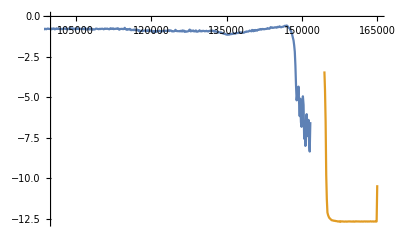

```mathematica
ListPlot[{hv6a[[2,1]],hv6b[[2,1]]},Joined->True,PlotRange->{{100000,165000},All}]
```

```mathematica
Dimensions[GetDevTimes["HV-LOWSIDE",jfile6]]
```

{1343}

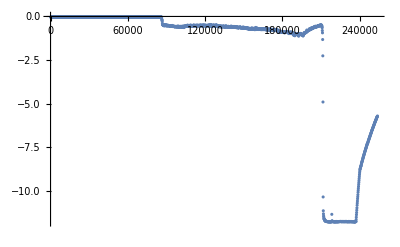

```mathematica
ShowHV[jfile5]
```

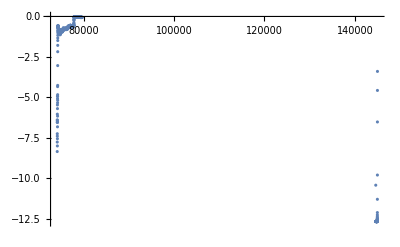

```mathematica
ShowHV[jfile6]
```

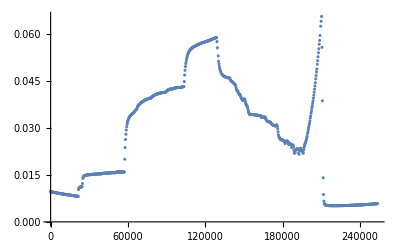

```mathematica
ShowPressure[jfile5]
```

InterpolatingFunction::dmval: Input value {210083.78562} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {210205.7596} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {219775.71843} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

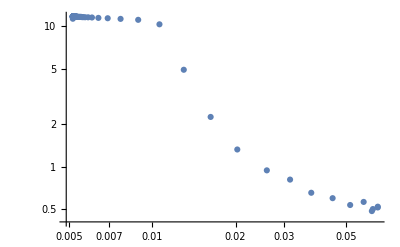

```mathematica
ShowPaschen[jfile5,210000,220000]
```

```mathematica
GetDevTimes["Command",jfile4]
```

{1658533342777}

```mathematica
ShowHV[jf_List]:=Module[{hv},
hv=GetDeviceData["HV-LOWSIDE",jf];
ListPlot[hv[[2,1]],PlotRange->All]
]
```

```mathematica
ShowHvRange[jf_List,take_]:=Module[{hv},
hv=GetDeviceDataRange["HV-LOWSIDE",jf,take];
ListPlot[hv[[2,1]],PlotRange->All]
]
```

```mathematica
ShowHvRangeInv[jf_List,take_]:=Module[{hv},
hv=GetDeviceDataRange["HV-LOWSIDE",jf,take];
ListPlot[{#[[1]],-#[[2]]}&/@hv[[2,1]],PlotRange->All]
]
```

```mathematica
ShowPressure[jf_List]:=Module[{pirani},
pirani=GetDeviceData["PIRANI",jf];
ListPlot[pirani[[2,3]],PlotRange->All]
]
```

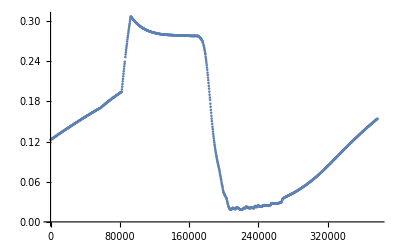

```mathematica
ShowPressure[jfile4]
```

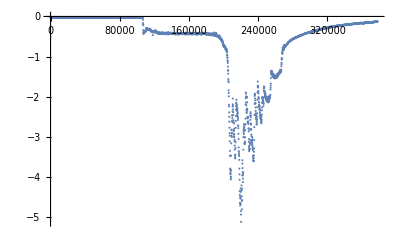

```mathematica
ShowHV[jfile4]
```

```mathematica
jfile3 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2022-07-22T16-23-42_Friday traversal.json"];
```

c:\git\FusorExperiments\logs\keep\fusor-2022-07-22T16-36-35_Friday traversal (1).json

```mathematica
FindBreaks[GetDevTimes["HV-LOWSIDE",jfile1]]
```

{1965}

```mathematica
FindBreaks[GetDevTimes["HV-LOWSIDE",jfile3]]
```

{}

```mathematica
hv3=GetDeviceData["HV-LOWSIDE",jfile3]
```

{{cw_avg,cwc_avg,nst_rms,variac_rms},{{{112.64187,-0.939731},{235.61576,-0.939731},{378.585408,-0.942073},{744.507719,-0.921585},6193,{772467.662116,-0.205692},{772588.636432,-0.195156},{772710.610535,-0.197497}},2,{{41,0.268995},6198,{1}}}}
 |  |  |  |

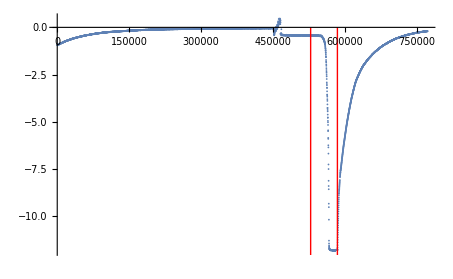

```mathematica
t1=528881;t2=584728;ListPlot[hv3[[2,1]],PlotRange->All,Epilog->{Red,Line[{{t1,0},{t1,-13}}],Line[{{t2,0},{t2,-13}}]}]
```

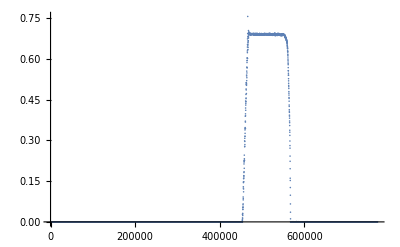

```mathematica
ListPlot[hv3[[2,2]],PlotRange->All]
```

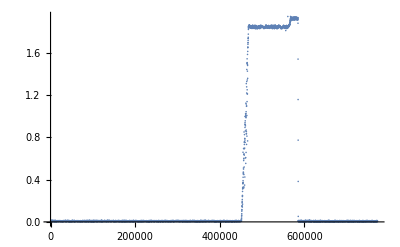

```mathematica
ListPlot[hv3[[2,3]],PlotRange->All]
```

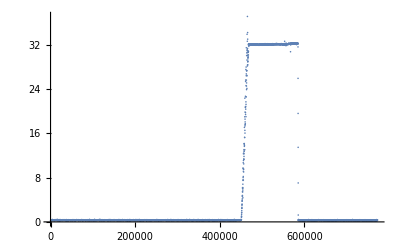

```mathematica
ListPlot[hv3[[2,4]],PlotRange->All]
```

```mathematica
ShowCommands[jf_List]:=Module[{cmd},
cmd=GetDeviceData["Command",jf];
TableForm[cmd[[2,3]]]
]
```

```mathematica
ShowCommands[jfile4]
```

31900. | TMP off
33910. | TMP off

```mathematica
cmd3=GetDeviceData["Command",jfile3];
```

```mathematica
TableForm[cmd3[[2,3]]]
```

17160. | TMP off
88461. | Set needle valve:10.0
88518. | Set needle valve:10.0
100150. | Set needle valve:50.0
100270. | Set needle valve:50.0
111400. | Set needle valve:0.0
129360. | Set needle valve:20.0
129460. | Set needle valve:20.0
168800. | Set needle valve:10.0
168870. | Set needle valve:10.0
185820. | Set needle valve:10.1
190240. | Set needle valve:15.0
190290. | Set needle valve:15.0
315750. | Set needle valve:0.0
325870. | Set needle valve:14.9
329690. | Set needle valve:10.0
329810. | Set needle valve:10.0
365537. | Set needle valve:20.0
365677. | Set needle valve:20.0
369607. | Set needle valve:10.0
369652. | Set needle valve:10.0
379870. | Set needle valve:0.0
387304. | Set needle valve:10.0
411978. | Set needle valve:10.5
414813. | Set needle valve:20.0
414925. | Set needle valve:20.0
422588. | Set needle valve:10.0
445863. | HV on
449088. | variac:set:40
505547. | Set needle valve:20.0
505883. | Set needle valve:20.0
512817. | Set needle valve:10.0
512939. | Set needle valve:10.0
528881. | Set needle valve:0.0
530421. | TMP on
584728. | variac:set:0

```mathematica
pirani3=GetDeviceData["PIRANI",jfile3]
```

{{p2,p3,p4},{{{23.13823,-764.},{326.451404,-764.},{629.764579,-764.},{934.078788,-764.},{1236.39093,-764.},2539,{771581.784165,-764.},{771889.101474,-764.},{772195.417751,-764.},{772493.725758,-764.}},{1},{1}}}
 |  |  |  |

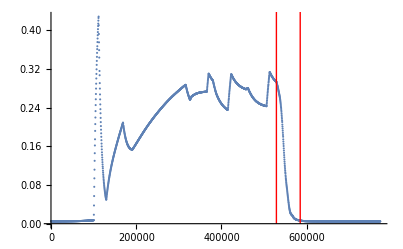

```mathematica
t1=528881;t2=584728;ListPlot[pirani3[[2,3]],PlotRange->All,Epilog->{Red,Line[{{t1,0},{t1,0.5}}],Line[{{t2,0},{t2,0.5}}]}]
```

```mathematica
pirani3a=Select[pirani3[[2,3]],#[[1]]>528881&&#[[1]]<584728&];
```

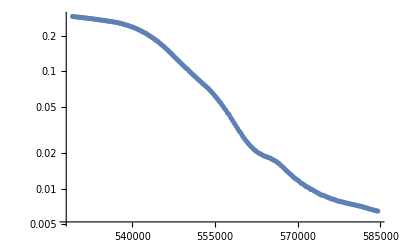

```mathematica
ListPlot[pirani3a,ScalingFunctions->{None,"Log"}]
```

```mathematica
hv3a=Select[hv3[[2,1]],#[[1]]>528881&&#[[1]]<584728&];
```

```mathematica
current3a=Select[hv3[[2,2]],#[[1]]>528881&&#[[1]]<584728&];
```

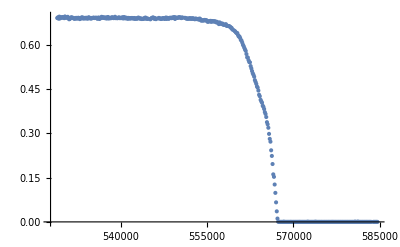

```mathematica
ListPlot[current3a]
```

```mathematica
hv3[[1]]
```

{cw_avg,cwc_avg,nst_rms,variac_rms}

```mathematica
sensor3=GetDeviceData["SENSORARRAY",jfile3];
```

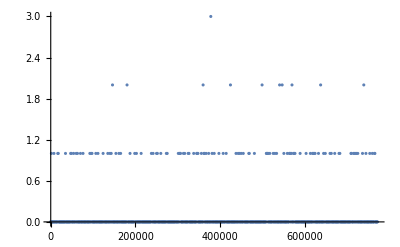

```mathematica
ListPlot[sensor3[[2,1]],PlotRange->All]
```

```mathematica
pressure3=Interpolation[pirani3a]
```

InterpolatingFunction[…]

```mathematica
ShowPaschen[jf_List,tmin_,tmax_]:=Module[{hv,hva,pirani,pirania,p,hvVsP},
hv=GetDeviceData["HV-LOWSIDE",jf];
pirani=GetDeviceData["PIRANI",jf];
hva=Select[hv[[2,1]],Between[#[[1]],{tmin,tmax}]&];
pirania=Select[pirani[[2,3]],Between[#[[1]],{tmin,tmax}]&];
p=Interpolation[pirania];
hvVsP=Table[{p[x[[1]]],-x[[2]]},{x,hva}];
ListPlot[hvVsP,PlotRange->All,ScalingFunctions->{"Log","Log"}]
]
```

InterpolatingFunction::dmval: Input value {170033.644392} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {269862.109797} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {269984.083485} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

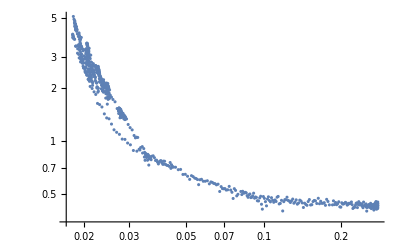

```mathematica
ShowPaschen[jfile4,170000,270000]
```

```mathematica
hvVsP3=Table[{pressure3[x[[1]]],-x[[2]]},{x,hv3a}];
```

InterpolatingFunction::dmval: Input value {528908.372523} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {529031.346415} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {529153.320518} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

```mathematica
currentVsP3=Table[{pressure3[x[[1]]],x[[2]]},{x,current3a}];
```

InterpolatingFunction::dmval: Input value {528908.372523} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {529031.346415} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {529153.320518} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

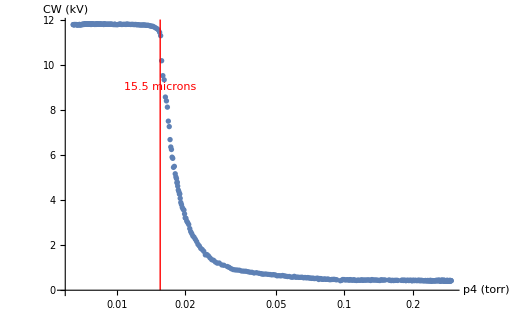

```mathematica
px=0.0155;ListPlot[hvVsP3,PlotRange->{All,All},
ScalingFunctions->{"Log",None},
Epilog->{Red,Line[{{Log[px],0},{Log[px],12}}],
Text[1000 px "microns",{Log[px],9}]},
AxesLabel->{"p4 (torr)","CW (kV)"}]
```

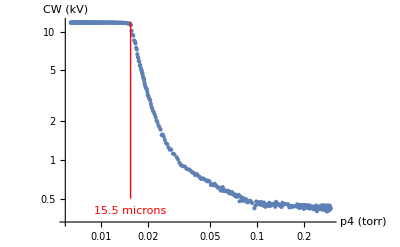

```mathematica
px=0.0155;ListPlot[hvVsP3,PlotRange->{All,All},
ScalingFunctions->{"Log","Log"},
Epilog->{Red,Line[{{Log[px],Log[0.5]},{Log[px],Log[12]}}],
Text[1000 px "microns",{Log[px],Log[0.4]}]},
AxesLabel->{"p4 (torr)","CW (kV)"}]
```

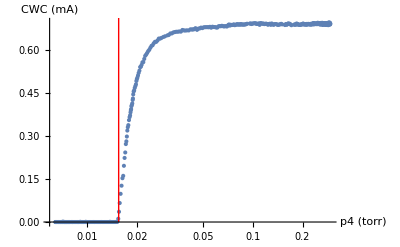

```mathematica
px=0.0155;ListPlot[currentVsP3,PlotRange->{All,All},
ScalingFunctions->{"Log",None},
Epilog->{Red,Line[{{Log[px],0},{Log[px],12}}],
Text[1000 px "microns",{Log[px],9}]},
AxesLabel->{"p4 (torr)","CWC (mA)"}]
```

```mathematica
hv1a=GetDeviceDataRange["HV-LOWSIDE",jfile1,1965];
```

```mathematica
hv1a[[1]]
```

{cw_avg,cwc_avg,n,nst_rms,variac_rms}

```mathematica
hv1b=GetDeviceDataRange["HV-LOWSIDE",jfile1,-1123];
```

```mathematica
hv1b[[2,1;;5,1]]
```

{{295186.2357947,-1.37718},{295186.2357947,0.},{295186.2357947,61},{295185.2360259,0.0561853},{295185.2360259,0.792467}}

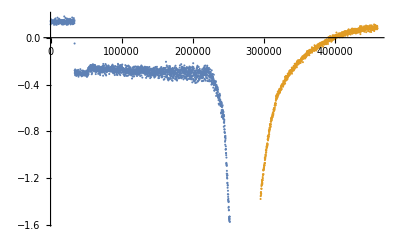

```mathematica
ListPlot[{hv1a[[2,1]],hv1b[[2,1]]},PlotRange->{All,All}]
```

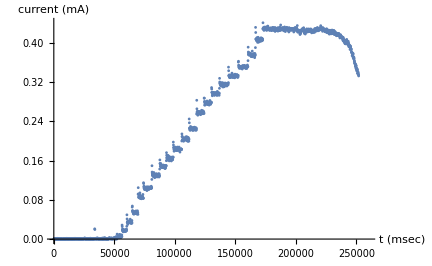

```mathematica
ListPlot[hv1a[[2,2]],PlotRange->{{0,260000},All},
AxesLabel->{"t (msec)","current (mA)"}]
```

```mathematica
cmd1=GetDeviceData["Command",jfile1];
```

```mathematica
cmd1[[2,3]]
```

{{20030.,#promote: tespelien},{25130.,TMP low},{33637.,variac:set:5.0},{33743.,variac:set:5.0},{45684.,variac:set:6.0},{52075.,variac:set:7.0},{56235.,variac:set:8.0},{60195.,variac:set:9.0},{64625.,variac:set:10.0},{69511.,variac:set:11.0},{73969.,variac:set:12.0},{80901.,variac:set:13.0},{87390.,variac:set:14.0},{92898.,variac:set:15.0},{98551.,variac:set:16.0},{105640.,variac:set:17.0},{111690.,variac:set:18.0},{117880.,variac:set:19.0},{124050.,variac:set:20.0},{130210.,variac:set:21.0},{136760.,variac:set:22.0},{144170.,variac:set:23.0},{152310.,variac:set:24.0},{160400.,variac:set:25.0},{166520.,variac:set:26.0},{172600.,variac:set:27.0},{181070.,TMP low},{200890.,TMP on},{287750.,variac:set:0.0}}

```mathematica
hv1a[[2,1;;5,-1]]
```

{{251974.162209,-1.5728},{251974.162209,0.332199},{251974.162209,60},{251974.162209,1.4788},{251974.162209,25.9156}}

```mathematica
FindBreaks[GetDevTimes["PIRANI",jfile1]]
```

{1779}

```mathematica
pirani1a = GetDeviceDataRange["PIRANI",jfile1,1779];
```

```mathematica
pirani1a[[1]]
```

{p2,p3,p4}

```mathematica
pirani1a[[2,1;;3,-1]]
```

{{257198.805419,-760.},{257263.871399,0.0223},{257339.948545,0.0223}}

```mathematica
ListDevices[jfile1]
```

{<reset>,PIRANI,HV-LOWSIDE,GAS,TMP,SENSORARRAY,HV-RELAY,RP,VARIAC,Heartbeat,Command,<promote>,Comment}

```mathematica
FindBreaks[GetDevTimes["GAS",jfile1]]
```

{251}

```mathematica
gas1a = GetDeviceDataRange["GAS",jfile1,251];
```

```mathematica
gas1a[[1]]
```

{nv_angle,nv_in,nv_ms,sol_in,sol_stat}

```mathematica
gas1a[[2,1,-1]]
```

{-443926.296146,0.}

```mathematica
FindBreaks[GetDevTimes["TMP",jfile1]]
```

{2184}

```mathematica
tmp1a = GetDeviceDataRange["TMP",jfile1,2184];
```

```mathematica
tmp1a[[1]]
```

{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp}

```mathematica
tmp1a[[2,1;;6,-1]]
```

{{257378.111965,False},{181106.809497,True},{257378.111965,1.43066},{257378.111965,128.174},{-174505.789641,False},{200923.196432,True}}

```mathematica
FindBreaks[GetDevTimes["HV-RELAY",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["RP",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["VARIAC",jfile1]]
```

{}

```mathematica
FindBreaks[GetDevTimes["SENSORARRAY",jfile1]]
```

{}

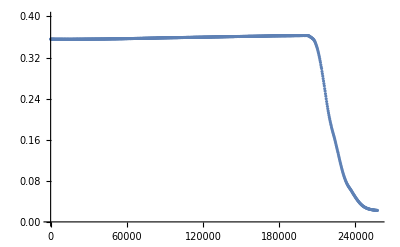

```mathematica
ListPlot[pirani1a[[2,3]],PlotRange->{All,{0,.4}}]
```

```mathematica
Take[pirani1a[[2,3]],-1]
```

{{257339.948545,0.0223}}

```mathematica
Take[hv1a[[2,1]],-1]
```

{{251974.162209,-1.5728}}

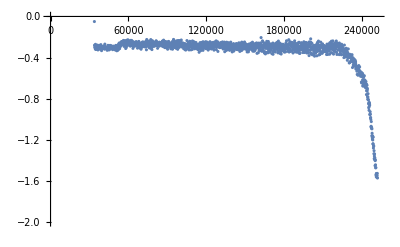

```mathematica
ListPlot[hv1a[[2,1]],PlotRange->{All,{-2,0}}]
```

```mathematica
hv1a[[2,1]]
```

{{59.0942366,0.112804},{183.064743,0.139055},{333.029066,0.145963},{456.9995727,0.125239},{583.9693658,0.128002},1955,{251597.251878,-1.54655},{251722.222147,-1.56796},{251847.192416,-1.5279},{251974.162209,-1.5728}}
 |  |  |  |

```mathematica
FindBreaks[hvTimes]
```

{1965}

```mathematica
Dimensions[hvTimes]
```

{3088}

```mathematica
jfile1 =Import["c:\\git\\FusorExperiments\\logs\\keep\\fusor-2021-06-03T16-25-12_repeat of 8kv plasma test.json"];
```

```mathematica
jfile2 =Import["C:\\git\\EpsIo\\Fusor\\logs\\fusor-2021-06-06T16-43-42_last take (1).json"];
```

```mathematica
hvTimes2=GetDevTimes["HV-LOWSIDE",jfile2];
```

```mathematica
hv2=GetDeviceData["HV-LOWSIDE",jfile2];
```

```mathematica
hv2[[1]]
```

{cw_avg,cwc_avg,n,nst_rms,variac_rms}

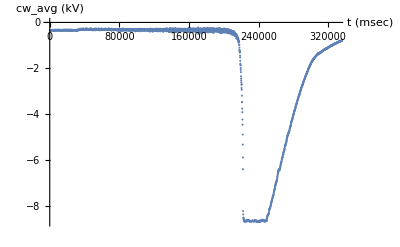

```mathematica
t2=240000;ListPlot[hv2[[2,1]],
PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,1]]" (kV)"}]
```

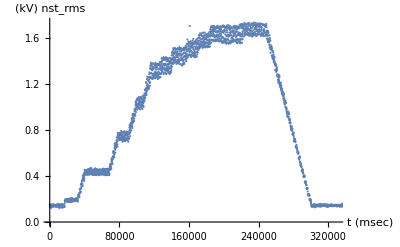

```mathematica
ListPlot[hv2[[2,4]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,4]]" (kV)"}]
```

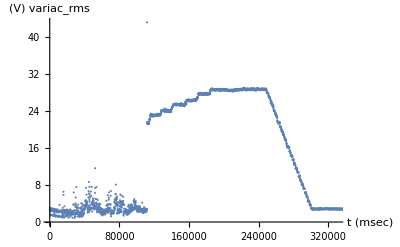

```mathematica
ListPlot[hv2[[2,5]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,5]]" (V)"}]
```

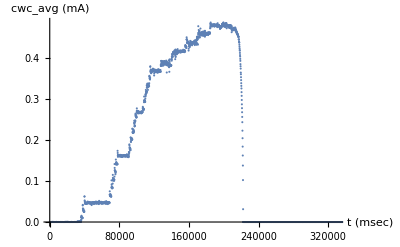

```mathematica
ListPlot[hv2[[2,2]],
PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",hv2[[1,2]]" (mA)"}]
```

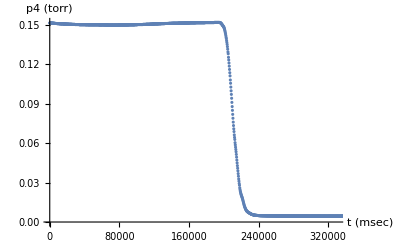

```mathematica
ListPlot[pirani2[[2,3]],PlotRange->{{0,330000},All},
AxesLabel->{"t (msec)",pirani2[[1,3]]" (torr)"}]
```

```mathematica
Take[pirani2[[2,3]],-2]
```

{{237795.158651,0.02218},{238081.445423,0.02215}}

```mathematica
pirani2=GetDeviceData["PIRANI",jfile2];
```

```mathematica
piraniTimes2=GetDevTimes["PIRANI",jfile2];
```

```mathematica
FindBreaks[piraniTimes2]
```

{}

```mathematica
cmd2=GetDeviceData["Command",jfile2]; cmd2[[1]]
```

{ip,observer,text}

```mathematica
tmp2=GetDeviceData["TMP",jfile2];
```

```mathematica
tmp2[[1]]
```

{error,lowspeed,pump_curr_amps,pump_freq,reset,tmp}

```mathematica
tmp2[[2,1,-1]]
```

{388380.669154,False}

```mathematica
MatrixForm[cmd2[[2,3]]]
```

(10000. | variac:set:5.0
31160. | variac:set:10.0
68702. | variac:set:15.0
90262. | variac:set:20.0
106680. | variac:set:25.0
127390. | variac:set:26.0
139670. | variac:set:27.0
155510. | variac:set:28.0
168880. | variac:set:29.0
183150. | variac:set:30.0
194230. | TMP on
242590. | variac:set:1.0
381563. | TMP off
387716. | variac:set:0.0)

```mathematica
cmd1=GetDeviceData["Command",jfile1];cmd1[[1]]
```

{ip,observer,text}

```mathematica
ListDevices[jfile1]
```

{<reset>,Comment,VARIAC,GAS,Heartbeat,TMP,HV-RELAY,PIRANI,RP,SENSORARRAY,HV-LOWSIDE,Login,Command,<promote>}

```mathematica
sensor2=GetDeviceData["SENSORARRAY",jfile2];
```

```mathematica
sensor2[[1]]
```

{gc1,gc2,gc3,pin,pnj}

```mathematica
tx=220000;
```

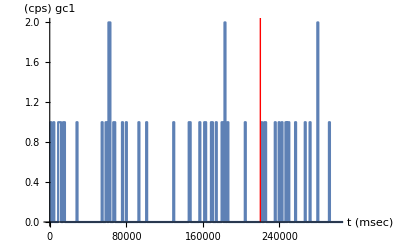

```mathematica
ListStepPlot[sensor2[[2,1]],PlotRange->{{0,300000},All},
Epilog->{Red,Line[{{tx,0},{tx,6}}]},
AxesLabel->{"t (msec)",sensor2[[1,1]]" (cps)"}]
```

```mathematica
sensor6=GetDeviceData["SENSORARRAY",jfile6]
```

{{gc1,gc2,gc3,hfm},{1}}
 |  |  |  |

```mathematica
ListStepPlot[sensor6[[2,1]],PlotRange->{{0,300000},All},
Epilog->{Red,Line[{{tx,0},{tx,6}}]},
AxesLabel->{"t (msec)",sensor6[[1,1]]" (cps)"}]
```

-Graphics-

```mathematica
pressure2=Interpolation[pirani2[[2,3]]]
```

InterpolatingFunction[…]

```mathematica
hvVsP2=Table[{pressure2[x[[1]]],-x[[2]]},{x,Drop[hv2[[2,1]],-1000]}];
```

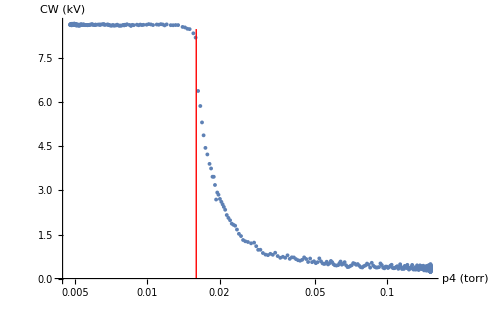

```mathematica
px=0.016;ListPlot[hvVsP2,PlotRange->{All,All},
ScalingFunctions->{"Log",None},
Epilog->{Red,Line[{{Log[px],0},{Log[px],8.5}}],
Text[1000 px "microns",{Log[px],9}]},
AxesLabel->{"p4 (torr)","CW (kV)"}]
```

```mathematica
current2=Interpolation[hv2[[2,2]]]
```

InterpolatingFunction[…]

```mathematica
hvVsCurrent2=Table[{current2[x[[1]]],-x[[2]]},{x,hv2[[2,1]]}];
```

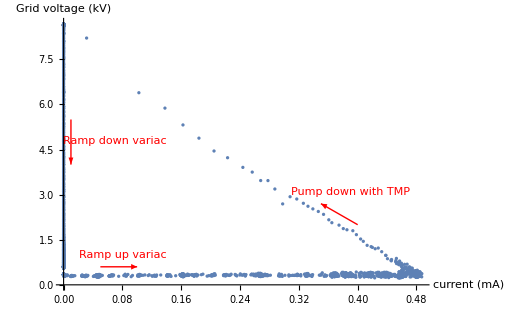

```mathematica
ListPlot[hvVsCurrent2,PlotRange->All,PlotStyle->Large,
AxesLabel->{"current (mA)","Grid voltage (kV)"},
Epilog->{Red,Thick,
Arrow[{{0.05,0.6},{0.1,0.6}}],Text["Ramp up variac",{0.08,1.0}],
Arrow[{{0.4,2},{0.35,2.7}}],Text["Pump down with TMP",{0.39,3.1}],
Arrow[{{0.01,5.5},{0.01,4}}],Text["Ramp down variac",{0.07,4.8}]
}]
```